```mathematica
(*собственные значения тестовой матрицы*)
evs=Table[i^3,{i,1,20}];
(*evs={0.5,1,1.7}*)
(*evs={0.37824855787278,0.8041219071526053,1.2958780928473947}*)
NN=Length@evs;
(*ω=(#⟦1⟧/#⟦2⟧&)@({#,Norm@#//N}&)@Table[1000/k,{k,1,NN}];*)
ω=#/(Norm@#)&@RandomReal[{-1000,1000},{NN}];
(*матрица отражения*)
H=IdentityMatrix@Length@ω-2KroneckerProduct[ω,ω];
dd=DiagonalMatrix@evs;
A=H.dd.H;
(*λ=Take[Reverse@λ,9]*)
ek=7;
sk=0;
(*выбираем собственные значения для интерполирования по ним*)
λ=Take[Reverse@evs,ek]~Join~Take[evs,sk];
NN=Length@λ;
α=1./λ
(*базисные функции Лагранжа*)
MatrixProduct:=Function[{list},
Last@FoldList[Dot,IdentityMatrix@Length@list⟦1⟧,list]
];
lagrange[AA_,λ_,i_]:=MatrixProduct@Table[(AA-λ⟦k⟧IdentityMatrix@Length@AA)/(λ⟦i⟧-λ⟦k⟧),{k,Complement[Range[Length@λ],{i}]}];
MatrixInterpolation[BB_,λ_,α_]:=Sum[α⟦q⟧lagrange[BB,λ,q],{q,1,Length@α}];
(*MatrixInterpolation[A,λ,α].A//MatrixForm*)
(*Eigenvalues@MatrixInterpolation[A,λ,α]*)
(*Print["Eigennvalues of the preconditioned matrix:",#]&@Eigenvalues@(MatrixInterpolation[A,λ,α].A);
Print["Eigennvalues of the not preconditioned matrix:",#]&@Eigenvalues@A;*)
ratio[A_]:=(Min[Abs[#]]/Max[Abs[#]])&@Eigenvalues@A;
Print["Ratio of the preconditioned matrix:",#]&@ratio[MatrixInterpolation[A,λ,α].A];
Print["Ratio of the not preconditioned matrix:",#]&@ratio@A;
```

{0.000125,0.000145794,0.000171468,0.000203542,0.000244141,0.000296296,0.000364431}

Ratio of the preconditioned matrix:0.00154966

Ratio of the not preconditioned matrix:0.000125

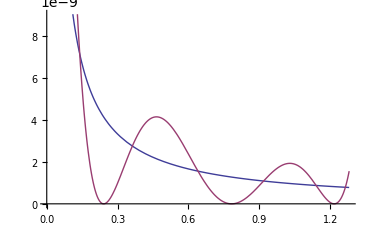

```mathematica
(*Интерполирование по чебыовским узлам*)
n=6;
{a,b}={Min@evs,Max@evs};
chebyshevD[n_]:=Table[(a+b)/2+(b-a)/2 Cos[(π+2π k)/(2n+2)],{k,0,n}];
dots=chebyshevD[6];

f=1./#&;

pts=Transpose[{dots,f/@dots}];
ip=InterpolatingPolynomial[pts,x];
Plot[{f[x],ip},{x,a,b}]
```

```mathematica
A//Eigenvalues
```

{1.7,1.,0.5}

```mathematica
fPARatio[k_]:=ratio[MatrixInterpolation[A,chebyshevD[k], f/@chebyshevD[k]].A];
nDots=Range[2,10];
res=fPARatio/@nDots;
listToPlot=Transpose[{nDots,res}]
```

{{2,7.03125×10^-9},{3,1.25701×10^-8},{4,1.95312×10^-8},{5,2.86077×10^-8},{6,3.82812×10^-8},{7,5.0185×10^-8},{8,6.32812×10^-8},{9,7.82781×10^-8},{10,9.45312×10^-8}}

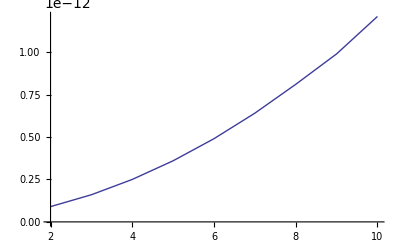

9.99873×10^-15

```mathematica
ListPlot[listToPlot,Joined->True]

ratio[A]
```

```mathematica
k=10;
precond=MatrixInterpolation[A,chebyshevD[k], f/@chebyshevD[k]];
A;
MatrixPlot[MatrixInterpolation[A,chebyshevD[k], f/@chebyshevD[k]].A];
MatrixPlot[MatrixInterpolation[A,chebyshevD[k], f/@chebyshevD[k]]];
MatrixPlot[A];
ratio@A
ratio@(precond.A)
```

7.8125×10^-10

9.45312×10^-8

```mathematica
precond
```

{{7.13239×10^-13,3.45838×10^-15,-5.4663×10^-15,-1.49839×10^-15,-3.78498×10^-15,5.38031×10^-15,8.2894×10^-15,1.96433×10^-15,6.21737×10^-15,1.3366×10^-15,«80»,2.58636×10^-15,1.92686×10^-15,9.71448×10^-16,-3.22042×10^-15,1.97034×10^-15,2.4338×10^-15,-3.60591×10^-15,-2.80578×10^-15,-3.12416×10^-15,-3.41732×10^-15},«98»,{«1»}}